```mathematica
CLear[m]

(*diagram of the paint*)
pts={{0,0.17,0},{-2.7,2,0},{0,3.83,0}};

courtGraph=Graphics3D[{Orange, Sphere[{0,2,2.13},.12],Black,Opacity[.1],Cuboid[{4.572,2.36,2.75},{4.572,1.64,3.23}],Black,Opacity[.7],Cuboid[{4.572,2.076,0},{4.572,1.924,2.75}],Black,Thickness[Large],Line[{{0,.17,0},{0,3.83,0}}],Line[{{0,.17,0},{4.572,0.17,0}}],Line[{{0,3.83,0},{4.572,3.83,0}}],Line[{{4.572,.17,0},{4.572,3.83,0}}],BSplineCurve[pts]},Boxed->False];

(*showing dimensions of court*)
arrows=Graphics3D[{Arrowheads[.02],Arrow[{{0,2,1.23},{0,2,2.13}}],Arrow[{{0,2,.91},{0,2,0}}],Text[Style[2.13m,Medium],{0,2,1.065}],Arrowheads[0.02],Arrow[{{1.8,-0.5,0},{0,-0.5,0}}],Arrow[{{2.72,-0.5,0},{4.572,-0.5,0}}],Text[Style[4.572m,Medium],{2.286,-0.5,0}],Arrowheads[0.02],Arrow[{{5,1.6,1.32},{5,1.6,0}}],Arrow[{{5,1.6,1.73},{5,1.6,3.05}}],Text[Style[3.05m,Medium],{5,1.6,1.525}]}];

Show[courtGraph,arrows]
```

CLear[m]

-Graphics3D-

```mathematica
(*diagram of hoop from a bird's eye view*)
hoop=Graphics[{Red,Annulus[{0,0},{.2285,.2365}]}];
(*dimensions of hoop*)
arrowing=Graphics[{Arrowheads[.02],Arrow[{{.07,0},{0,0}}],Arrow[{{.16,0},{.2285,0}}],Text[Style[.2285m,Medium],{.1143,0}],Arrowheads[0.02],Arrow[{{0,0.13},{0,.2365}}],Arrow[{{0,0.1},{0,0}}],Text[Style[.2365m,Medium],{0,.115}]}];
Show[hoop,arrowing]
```

-Graphics-

```mathematica
Clear[x,y,t]
(*Constants*)g=9.8; (*Acceleration due to gravity in m/s^2*)
initialVelocity=10; (*Initial velocity of the shot in m/s*)
angle=45; (*Launch angle in degrees*)

(*basketball constants in SI units*)
d=4.572;      (*meters between line and backboard*)
h=3.05;       (*height of the basket in meters*)

(*Convert angle to radians*)
angleRad=angle*Pi/180;

(*Randomly Generating the Release height of the ball based on the\
average height of an NBA player (6'6") *)
PlayerHeight=RandomReal[{1.9812,2.286}];

(*Accounting for air resistance*)
g=9.8;
m=RandomReal[{.6,.7}]; (*Required range of mass for official nba basketball*)
c=0.54; (*drag coefficient for an NBA basketball*)
ρ=1.226;(*assuming the free throw takes place at Delta Center in SLC at room temperature*)
r=RandomReal[{.12,.121}]; (*Range of radius of basketball as stated by the nba*)
A=Pi*r^2; (*cross sectional area used to calculate air resistance*)
mu=(c*ρ*A)/(2*m);
vsubt=Sqrt[g/mu]
timeForVT=1/Sqrt[g*mu]

(*System of differential equations*)
eqns={x'[t]==initialVelocity Cos[angleRad],y'[t]==initialVelocity Sin[angleRad]-g t,x[0]==0,y[0]==PlayerHeight};

(*Solve the system numerically using NDSolve*)
sol=NDSolve[eqns,{x,y},{t,timeForVT}]

(*Animate the free throw shot*)
Animate[Show[ParametricPlot[Evaluate[{x[t],y[t]}/. sol],{t,0,tmax},PlotStyle->Blue],Graphics[{Red,PointSize[0.02],Point[Evaluate[{x[tmax],y[tmax]}/. sol]]}],PlotRange->{{0,12},{0,5}},AspectRatio->1,Frame->True,AxesLabel->{"Horizontal Distance (m)","Vertical Distance (m)"},PlotLabel->StringForm["Time: `` s",NumberForm[tmax,{3,2}]]],{tmax,0.01,timeForVT,0.1}]

(*If this cell is producing an error in the simulation try running it individually*)
```

20.5085

2.0927

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

(0.230396 | 0.814925
0.224289 | 0.837114
0.218605 | 0.858879
0.213292 | 0.880274
0.208306 | 0.901342
0.203613 | 0.922116
0.199182 | 0.942629
0.194988 | 0.962905
0.191009 | 0.982967
0.187225 | 1.00283
0.18362 | 1.02252
0.18018 | 1.04204
0.176892 | 1.06141
0.173744 | 1.08064
0.170727 | 1.09974
0.167831 | 1.11872)

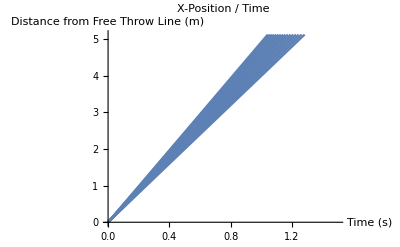

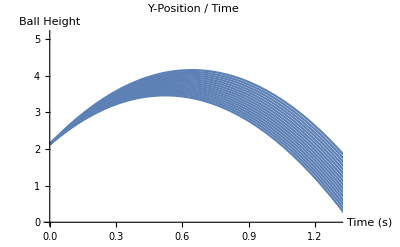

Miss: time = 0.814925 and vel = 6.5

Miss: time = 0.837114 and vel = 6.6

Miss: time = 0.858879 and vel = 6.7

Miss: time = 0.880274 and vel = 6.8

Miss: time = 0.901342 and vel = 6.9

Successful shot: time = 0.922116 and vel = 7.

Successful shot: time = 0.942629 and vel = 7.1

Successful shot: time = 0.962905 and vel = 7.2

Successful shot: time = 0.982967 and vel = 7.3

Miss: time = 1.00283 and vel = 7.4

Miss: time = 1.02252 and vel = 7.5

Miss: time = 1.04204 and vel = 7.6

Miss: time = 1.06141 and vel = 7.7

Miss: time = 1.08064 and vel = 7.8

Miss: time = 1.09974 and vel = 7.9

Miss: time = 1.11872 and vel = 8.

time 1: | time 2:
0.230396 | 0.814925
0.224289 | 0.837114
0.218605 | 0.858879
0.213292 | 0.880274
0.208306 | 0.901342
0.203613 | 0.922116
0.199182 | 0.942629
0.194988 | 0.962905
0.191009 | 0.982967
0.187225 | 1.00283
0.18362 | 1.02252
0.18018 | 1.04204
0.176892 | 1.06141
0.173744 | 1.08064
0.170727 | 1.09974
0.167831 | 1.11872

```mathematica
Clear["`*"]
(*Randomly Generating the Release height of the ball based on the average height of an nba player(6'6")*)
ReleaseHeight=2.13;
(*Plot of projectile motion*)
v0=Range[6.5,8,.1];(*initial velocity*)
x0=0;(*initial x-position*)
y0=ReleaseHeight;
g=9.8;
angledegrees=52;
θ=angledegrees*Pi/180;

(*ball characteristics*)
m=RandomReal[{.6,.7}]; (*Required range of mass for official nba basketball*)
r=RandomReal[{.749,.762}]; (*Range of radius of basketball as stated by the nba*)
A=Pi*r^2; (*cross sectional area used to calculate air resistance*)

(*basketball constants in SI units*)
d=4.421;      (*meters between line and center of basket*)
h=3.05;       (*height of the basket in meters*)
hoopradius=.4752/2;
frontend=3.964;
backend=4.421;

x[t_]=x0+v0*Cos[θ]*t; (*x-position of time*)
Plot[x[t],{t,0,2},PlotRange->All];
y[t_]=y0+v0*Sin[θ]*t-.5*g*t^2;
(*y-position of time*)
Plot[y[t],{t,0,2},PlotRange->All];
tf={};

tf={};
For[i=1,i<=Length[v0],i+=1,
AppendTo[tf,t/.Solve[y[t][[i]]==h,t]]
]
tf//MatrixForm

xplot=Plot[x[t],{t,0,2},PlotRange->{{0,1.5},{0,ReleaseHeight+3}},AxesLabel->{"Time (s)","Distance from Free Throw Line (m)"},PlotLabel->"X-Position / Time"]

Print[Plot[y[t],{t,0,2},PlotRange->{{0,1.3},{0,ReleaseHeight+3}},AxesLabel->{"Time (s)","Ball Height"},PlotLabel->"Y-Position / Time"]
]
Do[
If[(x[tf[[i]][[2]]][[i]]/.v0->v0[[i]])<backend&&frontend<(x[tf[[i]][[2]]][[i]]/.v0->v0[[12]]),Print["Successful shot: time = "<>ToString[tf[[i]][[2]]]<>" and vel = "<>ToString[v0[[i]]]],Print["Miss: time = "<>ToString[tf[[i]][[2]]]<>" and vel = "<>ToString[v0[[i]]]]],
{i,Length[v0]}
]
columnlabels={"time 1:","time 2:"};
tableGraphic=Grid[Prepend[tf,columnlabels],Frame->All,FrameStyle->Directive[Thickness[1],Black],Spacings->{2,2},ItemStyle->{Automatic,Automatic,{{1,1}->Bold,{1,2}->Bold}}]
```